```mathematica
Solve[I1+I2/(1+r)==c1+c2/(1+r),c1]
```

{{c1→(-c2+I1+I2+I1 r)/(1+r)}}

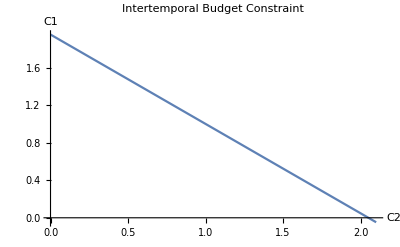

```mathematica
Plot[{(-c2+I1+I2+I1 r)/(1+r)}/.{I1->1,I2->1,r->0.05},{c2,0,2.1},AxesLabel->{"C2","C1"},PlotLabel->"Intertemporal Budget Constraint"]
```

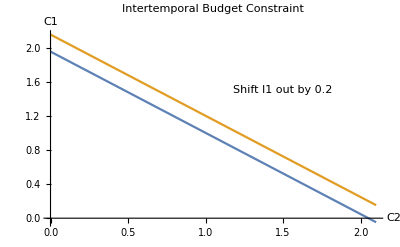

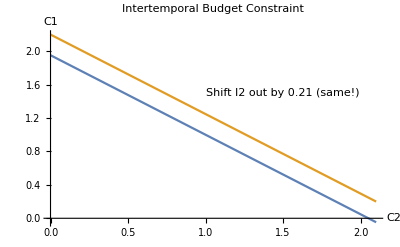

```mathematica
Show[Plot[{((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.05},((-c2+I1+I2+I1 r)/(1+r))/.{I1->1.2,I2->1,r->0.05}},{c2,0,2.1},AxesLabel->{"C2","C1"},PlotLabel->"Intertemporal Budget Constraint"],Graphics[Text["Shift I1 out by 0.2",{1.5,1.5}]]]
Show[Plot[{((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.05},((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1.2*1.05,r->0.05}},{c2,0,2.1},AxesLabel->{"C2","C1"},PlotLabel->"Intertemporal Budget Constraint"],Graphics[Text["Shift I2 out by 0.21 (same!)",{1.5,1.5}]]]
```

```mathematica
0.2*1.05
```

0.21

```mathematica
Solve[(c1+c1/(1+r)==150+100/(1+r))/.{r->0.05}]
```

{{c1→125.61}}

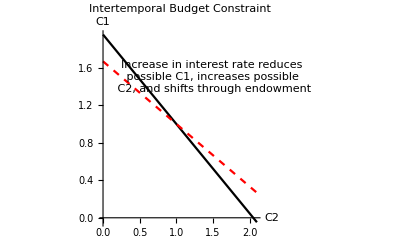

```mathematica
Show[Plot[{((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.05},((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.5}},{c2,0,2.1},AxesLabel->{"C2","C1"},PlotLabel->"Intertemporal Budget Constraint",PlotStyle->{Black,{Red,Dashed}}],Graphics[Text["Increase in interest rate reduces \n possible C1, increases possible \n C2, and shifts through endowment",{1.5,1.5}]]]
```

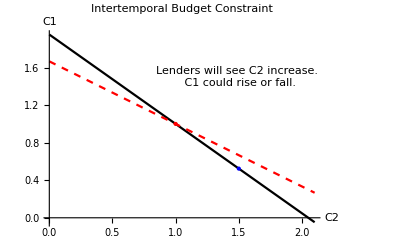

```mathematica
Show[Plot[{((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.05},((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.5}},{c2,0,2.1},AxesLabel->{"C2","C1"},PlotLabel->"Intertemporal Budget Constraint",PlotStyle->{Black,{Red,Dashed}}],Graphics[Text["Lenders will see C2 increase. \n C1 could rise or fall.",{1.5,1.5}]],Graphics[{PointSize[Large],Red,Point[{1,1}]}],Graphics[{PointSize[Large],Blue,Point[{1.5,0.52381}]}]]
```

```mathematica
((-0.5+1+1+1*0.05)/(1+0.05))
```

1.47619

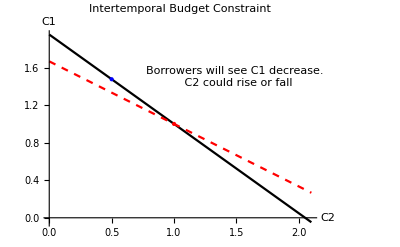

```mathematica
Show[Plot[{((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.05},((-c2+I1+I2+I1 r)/(1+r))/.{I1->1,I2->1,r->0.5}},{c2,0,2.1},AxesLabel->{"C2","C1"},PlotLabel->"Intertemporal Budget Constraint",PlotStyle->{Black,{Red,Dashed}}],Graphics[Text["Borrowers will see C1 decrease. \n C2 could rise or fall",{1.5,1.5}]],Graphics[{PointSize[Large],Red,Point[{1,1}]}],Graphics[{PointSize[Large],Blue,Point[{0.5,1.47619}]}]]
```

```mathematica
Solve[x*(0.7*(15*50000)+0.3*5000000)==3000000000000]
```

{{x→1.48148×10^6}}

```mathematica
1,481,481,
```